```mathematica
Import["/Users/wagner.palacio/Documents/Projeto/Repos/SystemModeling/Projects/Monkeypox/SEIQREpidemiologyModel.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
```

Importing from GitHub:  EpidemiologyModels.m

ToModelTime::shdw: Symbol ToModelTime appears in multiple contexts {SEIQREpidemiologyModel`,Global`}; definitions in context SEIQREpidemiologyModel` may shadow or be shadowed by other definitions.

```mathematica
Clear[modelSEIQR];
modelSEIQR = 
  SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
ModelGridTableForm[modelSEIQR]
```

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 100000
2 | β | 6.×10^-6
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==99999
2 | EP[0]==0
3 | IP[0]==1
4 | QP[0]==0
5 | RP[0]==0|>

## Getting Data

```mathematica
cievsPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Pernambuco/Monkeypox%20-%20Pernambuco.csv", 
   "Dataset", "HeaderLines" -> 1];
cievsRECData :=Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Recife/Monkeypox%20-%20Recife.csv", "Dataset", 
   "HeaderLines" -> 1];
owdPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/OWD/latest_deprecated.csv", "Dataset", "HeaderLines" -> 1];

dateFormat = {"Day", "/", "Month", "/", "Year"};
PEdataMap = cievsPEData // Normal;
RECdataMap = cievsRECData // Normal;
owdPEDataMap = Query[Select[StringContainsQ[ #Country, "Brazil"] && StringContainsQ[#Location, "Pernambuco"] && StringContainsQ[#Status, "confirmed"]&]] @ owdPEData;
```

#### Populações

```mathematica
(*pernambucoEntity = Entity["AdministrativeDivision", {"Pernambuco", "Brazil"}];
recifeEntity = Entity["City", {"Recife", "Pernambuco", "Brazil"}];
popProperty = "Population";*)

pernambucoPopulation = QuantityMagnitude[9674793]; (*IBGE 2022 - https://www.ibge.gov.br/cidades-e-estados/pe.html*)
recifePopulation =  QuantityMagnitude[1661017]; (*IBGE 2022 - https://www.ibge.gov.br/cidades-e-estados/pe.html*)
maleInfected = 82.6/100;(*Cievs/PE. Dados atualizados em 10.11.2022, 15h.*)
```

```mathematica
estimatedInitialSusceptiblePopulation = ((recifePopulation/pernambucoPopulation)*maleInfected)*recifePopulation
```

235552.

#### Confirmados

{Thu 21 Jul 2022→2,Fri 29 Jul 2022→4,Fri 5 Aug 2022→3,Sat 6 Aug 2022→3,Fri 12 Aug 2022→2,Tue 16 Aug 2022→1,Thu 18 Aug 2022→3,Wed 24 Aug 2022→4,Fri 26 Aug 2022→1,Mon 29 Aug 2022→1,Wed 31 Aug 2022→3,Thu 1 Sep 2022→14,Sun 4 Sep 2022→6,Tue 6 Sep 2022→1,Thu 8 Sep 2022→8,Fri 9 Sep 2022→4,Tue 13 Sep 2022→7,Wed 14 Sep 2022→23,Thu 15 Sep 2022→5,Fri 16 Sep 2022→12,Sat 17 Sep 2022→4,Tue 20 Sep 2022→7,Fri 23 Sep 2022→8,Tue 27 Sep 2022→2,Fri 30 Sep 2022→16,Tue 4 Oct 2022→10,Fri 7 Oct 2022→10,Tue 11 Oct 2022→0,Fri 14 Oct 2022→0,Tue 18 Oct 2022→1,Fri 21 Oct 2022→0,Tue 25 Oct 2022→3,Fri 28 Oct 2022→10,Tue 1 Nov 2022→8,Fri 4 Nov 2022→24,Tue 8 Nov 2022→3}

TimeSeries[…]

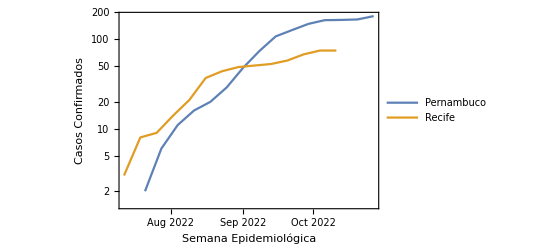

```mathematica
groupedByDateOWD = GroupBy[Normal[owdPEDataMap], FromDateString[#"Date_confirmation", {"Year", "-", "Month", "-", "Day"}]&,Length] // Normal;
groupedCievs= Map[FromDateString[#Inicio, dateFormat]-> #"Confirmados" &,PEdataMap];
confirmadosJoined = Union[groupedByDateOWD, Take[groupedCievs, {15,-1}]] 
totalJoinedSmoothed = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]], 7, "Align"->Left];

SmoothPeriod[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True], 7, "Align"->Left]
(*totalConfirmadosOWDPE=Smooth[Accumulate[TimeSeries[groupedByDateOWD, TemporalRegularity->True]]];*)
totalConfirmadosPE = 
    SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True]], 7, "Align"->Left];
totalConfirmadosREC = 
 SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #Confirmados} &,  RECdataMap],TemporalRegularity -> True]], 7, "Align"->Left];
DateListLogPlot[Tooltip[{totalJoinedSmoothed ,totalConfirmadosREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> False, GridLines -> Keys[confirmadosJoined],FrameLabel->{"Semana Epidemiológica","Casos Confirmados"}]
```

#### Prováveis

```mathematica
totalProvaveisPE =  SmoothPeriod[Accumulate[TimeSeries[ Map[{FromDateString[#Inicio, dateFormat], #"Prováveis"} &, PEdataMap], TemporalRegularity -> True]],7,"Align"->Left];
totalProvaveisREC = SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Prováveis"} &, RECdataMap], TemporalRegularity -> True]],7,"Align"->Left];
DateListLogPlot[Tooltip[{totalProvaveisPE, totalProvaveisREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> Automatic, GridLines -> Automatic];
```

#### Suspeitos

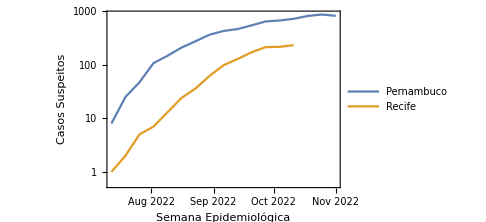

```mathematica
totalSuspeitosPE = 
  SmoothPeriod[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, 
      PEdataMap],TemporalRegularity -> True]],7,"Align"->Left];
totalSuspeitosREC = 
SmoothPeriod[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, RECdataMap], TemporalRegularity -> True]],7,"Align"->Left];
DateListLogPlot[Tooltip[{totalSuspeitosPE, totalSuspeitosREC} ], 
 Joined -> True, PlotLegends -> {"Pernambuco", "Recife"}, 
 PlotMarkers -> False, FrameLabel->{"Semana Epidemiológica","Casos Suspeitos"},ImageSize->Medium,GridLines -> False]
```

#### Notificados

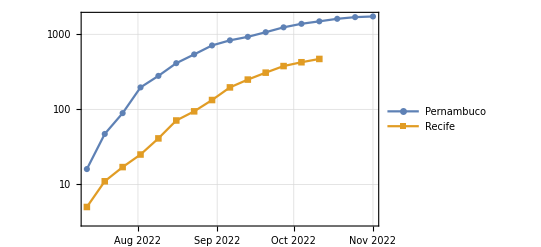

Keys::invrl: The argument joined is not a valid Association or a list of rules.

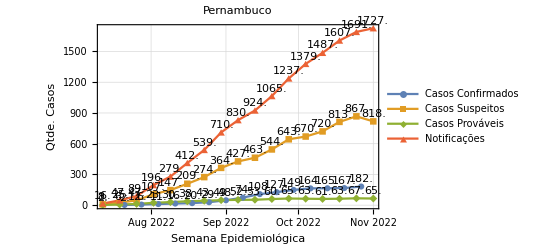

```mathematica
totalNotificadosPE = 
SmoothPeriod[Accumulate[
TimeSeries[
     Map[{FromDateString[#Inicio, dateFormat], #"Notificados"} &, 
      PEdataMap],TemporalRegularity -> True]],7,"Align"->Left];
totalNotificadosREC = 
SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Notificados"} &, RECdataMap],TemporalRegularity -> True]],7,"Align"->Left];
DateListLogPlot[Tooltip[{totalNotificadosPE, totalNotificadosREC} ],  Joined -> True, PlotLegends -> {"Pernambuco", "Recife"},  PlotMarkers -> Automatic, GridLines -> Automatic]

DateListPlot[{totalJoinedSmoothed ,totalSuspeitosPE, totalProvaveisPE, totalNotificadosPE}->{#2&},LabelingFunction->(Placed[Last@#1,Above]&), 
 Joined -> True, PlotLegends -> {"Casos Confirmados", "Casos Suspeitos", "Casos Prováveis", "Notificações" }, 
 PlotMarkers -> Automatic, GridLines -> Keys[joined],FrameLabel->{"Semana Epidemiológica","Qtde. Casos"}, PlotLabel->"Pernambuco"]
```

## Dados Literatura

Alguns dados que tirei de  artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

#### Periodo de Incubação

```mathematica
incubation = Range[5, 21];
incubationPeriod = Mean[incubation];
incubationPeriod
```

13

#### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0, 3];
rashPhase = Range[7, 21];
infectiousPeriod = Mean[Map[Median] @ {prodomalPhase, rashPhase}]
maxInfectiousPeriod = Max[prodomalPhase, rashPhase]
medianInfectiousPeriod = Flatten[ {prodomalPhase,rashPhase}]
```

31/4

21

{0,1,2,3,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

#### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/λ, sendo λ a média do período de infecção total.

## Modelos

```mathematica
initialInfected =  Normal[totalJoinedSmoothed][[1]][[2]]
initialExposed = Normal[totalProvaveisPE][[1]][[2]]
initialQuarantine = Normal[totalSuspeitosPE][[1]][[2]]
realEPData =  <|"Exposed"-> Ceiling[totalSuspeitosPE["Values"]] // Normal|>
realIPData = <|"Infected"-> Ceiling[totalJoinedSmoothed["Values"]] // Normal|>
realQPData = <|"Quarantine"-> Ceiling[totalProvaveisPE["Values"]] // Normal|>
allData = Join[realEPData,realIPData,realQPData]
lsFocusParams = {β, ζ, λ};
```

2

2

8

<|Exposed→{8,25,47,107,147,209,274,364,427,463,544,643,670,720,813,867,818}|>

<|Infected→{2,6,11,16,20,29,48,74,108,127,149,164,165,167,182}|>

<|Quarantine→{2,6,12,23,30,38,43,49,52,53,60,65,63,61,63,67,65}|>

<|Exposed→{8,25,47,107,147,209,274,364,427,463,544,643,670,720,813,867,818},Infected→{2,6,11,16,20,29,48,74,108,127,149,164,165,167,182},Quarantine→{2,6,12,23,30,38,43,49,52,53,60,65,63,61,63,67,65}|>

```mathematica
modelSEIQR = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation|>];
modelSEIQR = SetInitialConditions[modelSEIQR,
   <|SP[0] -> estimatedInitialSusceptiblePopulation -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>]; (* Subtrair do número da primeira semana epidemiológica*)
lsActualEquations = 
  Join[modelSEIQR["Equations"] //. 
    KeyDrop[modelSEIQR["RateRules"], lsFocusParams], 
   modelSEIQR["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations]
```

# | 1
1 | SP'[t]==0.2 QP[t]-4.24535×10^-6 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/ζ+4.24535×10^-6 β IP[t] SP[t]
3 | IP'[t]==EP[t]/ζ-IP[t]/λ
4 | QP'[t]==EP[t]/ζ-(0.2+1/λ) QP[t]
5 | RP'[t]==IP[t]/λ+QP[t]/λ
6 | SP[0]==235540.
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

```mathematica
aSol = Association@
  Flatten@ParametricNDSolve[lsActualEquations, 
    Head /@ Keys[modelSEIQR["Stocks"]], {t, 0,52}, lsFocusParams];
```

```mathematica
opts = {PlotRange -> All, PlotLegends -> None, PlotTheme -> "Detailed", 
   PerformanceGoal -> "Speed", ImageSize -> 400};
lsPopulationKeys = GetPopulationSymbols[modelSEIQR, __ ~~ "Population"];
Manipulate[
 DynamicModule[{lsPopulationPlots}, 
  lsPopulationPlots = 
   ParametricSolutionsPlots[modelSEIQR["Stocks"], 
    KeyTake[aSol, lsPopulationKeys], {contactRate, incubationPeriod, 
     infectionPeriod}, nWeeks,
    "LogPlot" -> popLogPlotQ, "Together" -> popTogetherQ, 
    "Derivatives" -> popDerivativesQ, "DerivativePrefix" -> "Δ",
     opts];
 
  Multicolumn[lsPopulationPlots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]],
   
 {{contactRate, 6.3, StringJoin["Contact rate of the infected population (β) ", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 1, 10, 1, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days"}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{infectionPeriod, 8, "Infection Period (λ) in days"}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week"}, 1, 52, 1, Appearance -> {"Open"}},
 {{popTogetherQ, True, "Plot populations together"}, {False, True}},
 {{popDerivativesQ, False, "Plot populations derivatives"}, {False, True}},
 {{popLogPlotQ, False, "LogPlot populations"}, {False, True}},
 {{nPlotColumns, 2, "Number of plot columns"}, Range[3]}, 
 ControlPlacement -> Left, ContinuousAction -> False]
```

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
Manipulate[
DynamicModule[{modelSEIQR=modelSEIQR,equations,aSol,lsPopulationPlots},
modelSEIQR = SetRateRules[modelSEIQR, <|NP[0] -> population|>];
modelSEIQR = SetInitialConditions[modelSEIQR,
   <|SP[0] ->  population -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>];
equations=Join[modelSEIQR["Equations"]//.KeyDrop[modelSEIQR["RateRules"],lsFocusParams],modelSEIQR["InitialConditions"]];
aSol=Association@Flatten@
ParametricNDSolve[equations,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams];

lsPopulationPlots=
ParametricSolutionsPlots[
modelSEIQR["Stocks"],
KeyTake[aSol,GetPopulationSymbols[modelSEIQR, __ ~~ "Population"]],
{contactRate, incubationPeriod,infectionPeriod},nWeeks,"Together"->False,opts];
    
Show[lsPopulationPlots⟦3⟧,ListPlot[PadRealData[realIPData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
],
{{population,estimatedInitialSusceptiblePopulation/100,"População"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"deslocamento de dados reais"},-100,100,1,Appearance->{"Open"}},
 {{contactRate, 0.01, StringJoin["Taxa de Contágio (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.01, 2, 0.01, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Período de Incubação (ζ) em dias"}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{infectionPeriod, 7, "Período de Infecção (λ) em dias"}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Semana Epidemiológica (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 2, "# de Colunas"}, Range[3]}, 
ControlPlacement->Left,ContinuousAction->False]
```

### Otimização de β

```mathematica
expostosJoined = Map[{FromDateString[#Inicio, dateFormat], #"Suspeitos"} &, PEdataMap];
```

```mathematica
totalInfectedOptimized = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],7,"Align"->Left]
```

TimeSeries[…]

```mathematica
firstDateInfected = First @ First@Normal[totalInfectedOptimized];
lastDateInfected = First @  Last@Normal[totalInfectedOptimized];
DateObject[First @ First@Normal[totalInfectedOptimized]]
```

Thu 21 Jul 2022 00:00:00GMT-3

```mathematica
ClearAll[modelSEIQR2];
modelSEIQR2 = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation/100|>];
modelSEIQR2 = SetInitialConditions[modelSEIQR2,
   <|SP[0] ->  estimatedInitialSusceptiblePopulation/100-initialExposed- initialInfected-initialQuarantine ,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>];
lsActualEquations2 = Join[modelSEIQR2["Equations"]//.KeyDrop[modelSEIQR2["RateRules"],lsFocusParams],modelSEIQR2["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations2]
asol2 = ParametricNDSolve[lsActualEquations2,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams];
```

# | 1
1 | SP'[t]==0.2 QP[t]-0.000424535 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/ζ+0.000424535 β IP[t] SP[t]
3 | IP'[t]==EP[t]/ζ-IP[t]/λ
4 | QP'[t]==EP[t]/ζ-(0.2+1/λ) QP[t]
5 | RP'[t]==IP[t]/λ+QP[t]/λ
6 | SP[0]==2343.52
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

#### Dados Totais, ajuste estatístico de β, ζ e λ

```mathematica
fitInfectedData={ToModelTime[firstDateInfected, #1], #2}& @@@ Normal[totalInfectedOptimized] //Echo[#, "", Multicolumn]&;
(*fitExposedData={toModelTime[firstDateExposed, #1], #2}& @@@ Normal[totalExpostosOptimized] //Echo[#, "", Multicolumn]&;*)
```

{0,2} | {28,20} | {56,108} | {84,165}
{7,6} | {35,29} | {63,127} | {91,167}
{14,11} | {42,48} | {70,149} | {98,182}
{21,16} | {49,74} | {77,164} |

```mathematica
infectedSol= IP[β,ζ,λ] /.asol2;
exposedSol = EP[β,ζ,λ] /.asol2;
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.432795 | 0.144859 | 2.98769 | 0.0113227
ζ | 5. | 6.2881 | 0.795153 | 0.441969
λ | 9.09259 | 1.48665 | 6.11614 | 0.0000520681

0.987511

0.984389

{β→0.432795,ζ→5.,λ→9.09259}

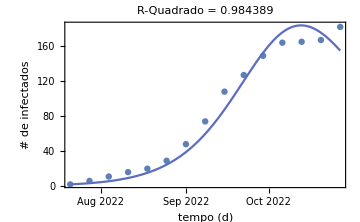

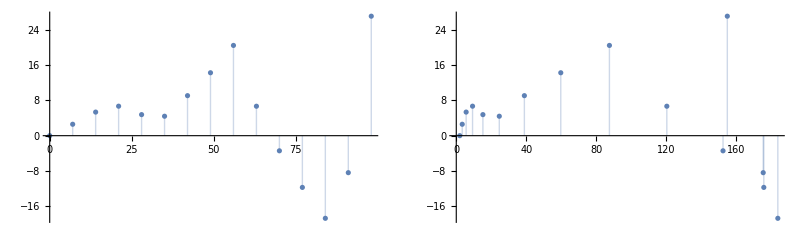

```mathematica
fitInfected=NonlinearModelFit[fitInfectedData,{infectedSol[t],5<=ζ<=21 && 0<=λ<=21 } ,{{β, 1.22}, {ζ,10},{λ,14}},t, Method->Automatic];
fitInfected["ParameterTable"]
fitInfected["RSquared"]
fitInfected["AdjustedRSquared"]
(*fitInfected["EstimatedVariance"]*)
fitInfected["BestFitParameters"]
(*fitInfected["Data"]*)
(*fitInfected["BestFit"]*)
FitWithDataPlot[fitInfected,{firstDateInfected,lastDateInfected} ]
ResidualsPlot[fitInfected]
(*ModelSensitivityPlot[ infectedSol,fitInfected,{{0,100},{-15,190}},{0.1,1,1}]*)
```

#### Ajuste estatístico, só β

```mathematica
lsActualEquations3 = Join[modelSEIQR2["Equations"]//.KeyDrop[modelSEIQR2["RateRules"],{β}],modelSEIQR2["InitialConditions"]];
ResourceFunction["GridTableForm"][List /@ lsActualEquations3]
asol3 = ParametricNDSolve[lsActualEquations3,{SP,EP,IP,QP, RP},{t,0,120},{β}];
```

# | 1
1 | SP'[t]==0.2 QP[t]-0.000424535 β IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/13+0.000424535 β IP[t] SP[t]
3 | IP'[t]==EP[t]/13-(4 IP[t])/31
4 | QP'[t]==EP[t]/13-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | SP[0]==2343.52
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

```mathematica
totalInfectedOptimized2 = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],21, "Align"-> Left] // Normal
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfected2 = First @ First@Normal[totalInfectedOptimized2]
lastDateInfected2 = First @  Last@ Normal[totalInfectedOptimized2]
fitInfectedData2={ToModelTime[firstDateInfected2, #1], #2}& @@@ Normal[totalInfectedOptimized2] //Echo[#, "", Multicolumn]&;
```

{{Thu 21 Jul 2022 00:00:00GMT-3,8},{Thu 11 Aug 2022 00:00:00GMT-3,23},{Thu 1 Sep 2022 00:00:00GMT-3,77},{Thu 22 Sep 2022 00:00:00GMT-3,147},{Thu 13 Oct 2022 00:00:00GMT-3,171}}

Thu 21 Jul 2022 00:00:00GMT-3

Thu 13 Oct 2022 00:00:00GMT-3

{0,8} | {42,77} | {84,171}
{21,23} | {63,147} |

{{Thu 21 Jul 2022 00:00:00GMT-3,8},{Thu 11 Aug 2022 00:00:00GMT-3,23},{Thu 1 Sep 2022 00:00:00GMT-3,77},{Thu 22 Sep 2022 00:00:00GMT-3,147},{Thu 13 Oct 2022 00:00:00GMT-3,171}}

NonlinearModelFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.680064 | 0.0220259 | 30.8756 | 6.5563×10^-6

0.974293

0.967866

{β→0.680064}

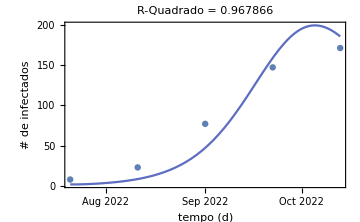

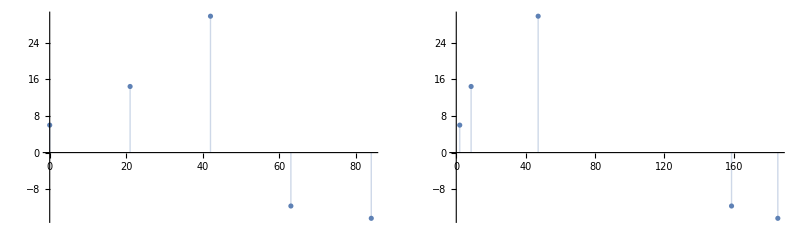

ModelSensitivityPlot[ParametricFunction[<>][β],FittedModel[InterpolatingFunction[…][t]],{{0,84},{-15,180}},{0.1}]

```mathematica
solution := ParametricNDSolve[lsActualEquations3,{SP,EP,IP,QP, RP},{t,First@First@fitInfectedData2,First@Last@fitInfectedData2},{β}];
{susceptible,infectedSol2}= {SP[β],IP[β]} /.solution;
current = Take[totalInfectedOptimized2,5]
fitInfected2=NonlinearModelFit[{ToModelTime[First@First@Normal[current], #1], #2}& @@@ Normal[current],infectedSol2[t],{{β,1}},t, Method->"QuasiNewton"];
fitInfected2["ParameterTable"]
fitInfected2["RSquared"]
fitInfected2["AdjustedRSquared"]
fitInfected2["BestFitParameters"]
FitWithDataPlot[fitInfected2,{First@First@Normal[current],First@Last@Normal[current]} ]
ResidualsPlot[fitInfected2]
ModelSensitivityPlot[ infectedSol2,fitInfected2,{{First@First@fitInfectedData2,First@Last@fitInfectedData2},{-15,180}},{0.1}]

(*susceptible=SP[N[First@Values[fitInfected2["BestFitParameters"]]]][84] /.solution*)
```

#### Com β Dinâmico

```mathematica
ClearAll[modelSEIQRDynamicBeta];
modelSEIQRDynamicBeta = With[{contactRate=ToExpression["Global`"<>"β"]},
model = SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
lsRepRules={
contactRate -> contactRate[t]
};
(*model["Rates"] = KeyDrop[model["Rates"], {contactRate}];*)
model["Rates"]=KeyMap[#/. lsRepRules&,model["Rates"]];
model["Equations"]=Map[#/. lsRepRules&,model["Equations"]];
model["RateRules"]=Association[Normal[model["RateRules"]]/. lsRepRules];
model["RateRules"]=KeyDrop[model["RateRules"],{contactRate[t]}];
AppendTo[model["Stocks"],NIP[t]->"Newly Infected Population"];model["InitialConditions"]=ReplacePart[model["InitialConditions"],3-> IP[t /; t<=0]==initialInfected];
(*AppendTo[modelSEIQRDynamicBeta["InitialConditions"], NIP[t/; IP[-1+t]+IP[t]===0]==1];*)
AppendTo[model["InitialConditions"], NIP[t /; t<=0]==initialInfected];
AppendTo[model["Equations"], NIP'[t]==IP[t]-IP[t-1]];
AppendTo[model["Equations"], ρ'[t]==((NIP[t-3] +NIP[t-2]+ NIP[t-1])/(NIP[t-3-ζ] + NIP[t-2-ζ]+NIP[t-1-ζ]))];
AppendTo[model["Equations"], β'[t]==((ρ[t-6] + ρ[t-5] +ρ[t-4] + ρ[t-3]+ ρ[t-2]+ρ[t])/7)/10 ];
AppendTo[model["InitialConditions"], ρ[t /; t<=0]==1];
AppendTo[model["InitialConditions"],  β[t /; t<=0]==0.001];
model];
```

```mathematica
modelSEIQRDynamicBeta = SetRateRules[modelSEIQRDynamicBeta, 
<|NP[0] -> Round[estimatedInitialSusceptiblePopulation/100],
λ-> 7|>
];
modelSEIQRDynamicBeta = SetInitialConditions[modelSEIQRDynamicBeta,
   <|
SP[0] ->  Round[estimatedInitialSusceptiblePopulation/100]-initialExposed- initialInfected-initialQuarantine ,
EP[0] -> initialExposed,
QP[0] -> initialQuarantine
    |>];
```

```mathematica
lsActualEquationsDynamicBeta = Join[modelSEIQRDynamicBeta["Equations"]//.KeyDrop[modelSEIQRDynamicBeta["RateRules"], {α1,α2}],modelSEIQRDynamicBeta["InitialConditions"]]
ModelGridTableForm[modelSEIQRDynamicBeta]
```

{SP'[t]==0.2 QP[t]-(IP[t] SP[t] β[t])/2356,EP'[t]==-((α1+α2) EP[t])+(IP[t] SP[t] β[t])/2356,IP'[t]==α1 EP[t]-IP[t]/7,QP'[t]==α2 EP[t]-0.342857 QP[t],RP'[t]==IP[t]/7+QP[t]/7,NIP'[t]==-IP[-1+t]+IP[t],ρ'[t]==(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t]),β'[t]==1/70 (ρ[-6+t]+ρ[-5+t]+ρ[-4+t]+ρ[-3+t]+ρ[-2+t]+ρ[t]),SP[0]==2344,EP[0]==2,IP[t/;t≤0]==2,QP[0]==8,RP[0]==0,NIP[t/;t≤0]==2,ρ[t/;t≤0]==1,β[t/;t≤0]==0.001}

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population
7 | NIP[t] | Newly Infected Population,Rates→# | Symbol | Description
1 | β[t] | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(IP[t] SP[t] β[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(IP[t] SP[t] β[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t]
6 | NIP'[t]==-IP[-1+t]+IP[t]
7 | ρ'[t]==(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-3+t-ζ]+NIP[-2+t-ζ]+NIP[-1+t-ζ])
8 | β'[t]==1/70 (ρ[-6+t]+ρ[-5+t]+ρ[-4+t]+ρ[-3+t]+ρ[-2+t]+ρ[t]),RateRules→# | Symbol | Value
1 | NP[0] | 2356
2 | α1 | 1/ζ
3 | α2 | 1/ζ
4 | φ | 0.2
5 | τ | γ
6 | γ | 1/λ
7 | ζ | 13
8 | λ | 7,InitialConditions→# | Equation
1 | SP[0]==2344
2 | EP[0]==2
3 | IP[t/;t≤0]==2
4 | QP[0]==8
5 | RP[0]==0
6 | NIP[t/;t≤0]==2
7 | ρ[t/;t≤0]==1
8 | β[t/;t≤0]==0.001|>

```mathematica
asolDynamicBeta = Association@Flatten@ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP, NIP,ρ, β},{t,0,100},{α1, α2}, Method->"StiffnessSwitching", MaxSteps->Infinity]
```

<|SP→ParametricFunction[<>],EP→ParametricFunction[<>],IP→ParametricFunction[<>],QP→ParametricFunction[<>],RP→ParametricFunction[<>],NIP→ParametricFunction[<>],ρ→ParametricFunction[<>],β→ParametricFunction[<>]|>

```mathematica
ResourceFunction["GridTableForm"][List /@ lsActualEquationsDynamicBeta]
```

# | 1
1 | SP'[t]==0.2 QP[t]-(IP[t] SP[t] β[t])/2356
2 | EP'[t]==-((α1+α2) EP[t])+(IP[t] SP[t] β[t])/2356
3 | IP'[t]==α1 EP[t]-IP[t]/7
4 | QP'[t]==α2 EP[t]-0.342857 QP[t]
5 | RP'[t]==IP[t]/7+QP[t]/7
6 | NIP'[t]==-IP[-1+t]+IP[t]
7 | ρ'[t]==(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])
8 | β'[t]==1/70 (ρ[-6+t]+ρ[-5+t]+ρ[-4+t]+ρ[-3+t]+ρ[-2+t]+ρ[t])
9 | SP[0]==2344
10 | EP[0]==2
11 | IP[t/;t≤0]==2
12 | QP[0]==8
13 | RP[0]==0
14 | NIP[t/;t≤0]==2
15 | ρ[t/;t≤0]==1
16 | β[t/;t≤0]==0.001

```mathematica
allValues =Map[ParametricFunctionValues[#,<| α1->0.004, α2-> 0.004|>, {0,100,1}]&, asolDynamicBeta]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

<|SP→{{0,2344.},{1,2345.27},{2,2346.},{3,2346.32},{4,2346.3},{5,2346.01},{6,2345.48},{7,2344.71},{8,2343.71},{9,2342.5},{10,2341.08},{11,2339.45},{12,2337.59},{13,2335.49},{14,2333.1},{15,2330.39},{16,2327.26},{17,2323.63},{18,2319.38},{19,2314.36},{20,2308.37},{21,2301.16},{22,2292.42},{23,2281.76},{24,2268.64},{25,2252.41},{26,2232.19},{27,2206.85},{28,2174.9},{29,2134.39},{30,2082.78},{31,2016.8},{32,1932.34},{33,1824.46},{34,1687.71},{35,1517.09},{36,1310.02},{37,1069.69},{38,808.906},{39,551.971},{40,329.887},{41,167.619},{42,70.9213},{43,25.3187},{44,8.61113},{45,3.78694},{46,2.52307},{47,2.06297},{48,1.77289},{49,1.54455},{50,1.35761},{51,1.20316},{52,1.07472},{53,0.967203},{54,0.876594},{55,0.799697},{56,0.733977},{57,0.677412},{58,0.628389},{59,0.585612},{60,0.548041},{61,0.514834},{62,0.485308},{63,0.458907},{64,0.435174},{65,0.413734},{66,0.394274},{67,0.376535},{68,0.360301},{69,0.345388},{70,0.331641},{71,0.318928},{72,0.307135},{73,0.296166},{74,0.285936},{75,0.276372},{76,0.267411},{77,0.258995},{78,0.251077},{79,0.243612},{80,0.236563},{81,0.229894},{82,0.223576},{83,0.217581},{84,0.211885},{85,0.206466},{86,0.201303},{87,0.196378},{88,0.191676},{89,0.187182},{90,0.182881},{91,0.178761},{92,0.174812},{93,0.171023},{94,0.167383},{95,0.163885},{96,0.16052},{97,0.157281},{98,0.154161},{99,0.151154},{100,0.148252}},EP→{{0,2.},{1,2.06779},{2,2.28532},{3,2.63488},{4,3.11231},{5,3.72324},{6,4.47783},{7,5.38812},{8,6.46563},{9,7.71657},{10,9.1453},{11,10.7592},{12,12.5727},{13,14.6104},{14,16.91},{15,19.5245},{16,22.5247},{17,26.003},{18,30.0773},{19,34.897},{20,40.6513},{21,47.58},{22,55.9883},{23,66.2668},{24,78.9183},{25,94.5937},{26,114.14},{27,138.665},{28,169.619},{29,208.902},{30,258.99},{31,323.072},{32,405.152},{33,510.033},{34,642.995},{35,808.846},{36,1009.93},{37,1242.87},{38,1494.69},{39,1741.09},{40,1951.27},{41,2100.66},{42,2184.},{43,2216.16},{44,2219.59},{45,2211.36},{46,2199.8},{47,2187.61},{48,2175.42},{49,2163.29},{50,2151.23},{51,2139.23},{52,2127.3},{53,2115.43},{54,2103.63},{55,2091.88},{56,2080.19},{57,2068.56},{58,2057.},{59,2045.49},{60,2034.04},{61,2022.66},{62,2011.34},{63,2000.07},{64,1988.87},{65,1977.73},{66,1966.65},{67,1955.63},{68,1944.67},{69,1933.77},{70,1922.93},{71,1912.16},{72,1901.44},{73,1890.78},{74,1880.18},{75,1869.63},{76,1859.15},{77,1848.73},{78,1838.36},{79,1828.05},{80,1817.8},{81,1807.6},{82,1797.46},{83,1787.38},{84,1777.36},{85,1767.39},{86,1757.48},{87,1747.62},{88,1737.81},{89,1728.07},{90,1718.37},{91,1708.73},{92,1699.15},{93,1689.62},{94,1680.14},{95,1670.71},{96,1661.34},{97,1652.02},{98,1642.75},{99,1633.54},{100,1624.37}},IP→{{0,2.},{1,1.74129},{2,1.51757},{3,1.32469},{4,1.15904},{5,1.01747},{6,0.897291},{7,0.796219},{8,0.712311},{9,0.643919},{10,0.589632},{11,0.548248},{12,0.518763},{13,0.500381},{14,0.492527},{15,0.494873},{16,0.507362},{17,0.530252},{18,0.564155},{19,0.610102},{20,0.669615},{21,0.744811},{22,0.83854},{23,0.954564},{24,1.09781},{25,1.27468},{26,1.49352},{27,1.76519},{28,2.10387},{29,2.52805},{30,3.06194},{31,3.73705},{32,4.59411},{33,5.68493},{34,7.07341},{35,8.83415},{36,11.0459},{37,13.7758},{38,17.0525},{39,20.8303},{40,24.964},{41,29.22},{42,33.3383},{43,37.1146},{44,40.4467},{45,43.3219},{46,45.7758},{47,47.8584},{48,49.6182},{49,51.0985},{50,52.3366},{51,53.3651},{52,54.212},{53,54.9019},{54,55.4558},{55,55.8921},{56,56.2266},{57,56.4731},{58,56.6436},{59,56.7484},{60,56.7965},{61,56.7956},{62,56.7525},{63,56.6731},{64,56.5624},{65,56.4247},{66,56.264},{67,56.0835},{68,55.8861},{69,55.6742},{70,55.45},{71,55.2154},{72,54.9719},{73,54.7211},{74,54.4639},{75,54.2017},{76,53.9351},{77,53.6651},{78,53.3922},{79,53.1172},{80,52.8404},{81,52.5624},{82,52.2835},{83,52.0041},{84,51.7244},{85,51.4446},{86,51.1651},{87,50.8859},{88,50.6072},{89,50.3293},{90,50.052},{91,49.7757},{92,49.5003},{93,49.226},{94,48.9527},{95,48.6806},{96,48.4097},{97,48.14},{98,47.8716},{99,47.6044},{100,47.3386}},QP→{{0,8.},{1,5.68477},{2,4.04206},{3,2.87714},{4,2.05176},{5,1.46781},{6,1.05568},{7,0.766003},{8,0.563789},{9,0.424228},{10,0.329729},{11,0.267826},{12,0.229708},{13,0.209188},{14,0.20198},{15,0.205198},{16,0.217004},{17,0.236368},{18,0.262921},{19,0.296849},{20,0.338864},{21,0.390196},{22,0.452643},{23,0.52866},{24,0.621506},{25,0.735448},{26,0.876057},{27,1.0506},{28,1.26857},{29,1.54239},{30,1.8883},{31,2.32746},{32,2.88712},{33,3.60164},{34,4.5127},{35,5.6673},{36,7.11142},{37,8.87646},{38,10.9571},{39,13.2851},{40,15.7155},{41,18.0481},{42,20.0895},{43,21.7229},{44,22.9337},{45,23.7803},{46,24.346},{47,24.7068},{48,24.9217},{49,25.0329},{50,25.071},{51,25.0572},{52,25.007},{53,24.931},{54,24.837},{55,24.7304},{56,24.6151},{57,24.4938},{58,24.3684},{59,24.2404},{60,24.1106},{61,23.9799},{62,23.8487},{63,23.7173},{64,23.586},{65,23.455},{66,23.3245},{67,23.1944},{68,23.0648},{69,22.9359},{70,22.8076},{71,22.6799},{72,22.5529},{73,22.4265},{74,22.3009},{75,22.1759},{76,22.0516},{77,21.928},{78,21.8051},{79,21.6828},{80,21.5612},{81,21.4403},{82,21.3201},{83,21.2005},{84,21.0817},{85,20.9634},{86,20.8458},{87,20.7289},{88,20.6127},{89,20.497},{90,20.3821},{91,20.2678},{92,20.1541},{93,20.041},{94,19.9286},{95,19.8168},{96,19.7056},{97,19.5951},{98,19.4852},{99,19.3759},{100,19.2672}},RP→{{0,0.},{1,1.23484},{2,2.1553},{3,2.84744},{4,3.37322},{5,3.7774},{6,4.09247},{7,4.34211},{8,4.54378},{9,4.71042},{10,4.85177},{11,4.97526},{12,5.08663},{13,5.19047},{14,5.2905},{15,5.38988},{16,5.49141},{17,5.5977},{18,5.71131},{19,5.83493},{20,5.97147},{21,6.12425},{22,6.29716},{23,6.49487},{24,6.72304},{25,6.9887},{26,7.30062},{27,7.66984},{28,8.11038},{29,8.64011},{30,9.282},{31,10.0656},{32,11.0291},{33,12.2216},{34,13.7059},{35,15.5612},{36,17.8845},{37,20.7891},{38,24.3978},{39,28.8277},{40,34.1671},{41,40.4517},{42,47.6517},{43,55.6807},{44,64.4208},{45,73.7501},{46,83.5594},{47,93.7575},{48,104.27},{49,115.036},{50,126.007},{51,137.14},{52,148.403},{53,159.766},{54,171.205},{55,182.7},{56,194.235},{57,205.793},{58,217.364},{59,228.937},{60,240.501},{61,252.05},{62,263.578},{63,275.078},{64,286.545},{65,297.976},{66,309.367},{67,320.715},{68,332.017},{69,343.271},{70,354.476},{71,365.63},{72,376.732},{73,387.78},{74,398.774},{75,409.712},{76,420.596},{77,431.423},{78,442.194},{79,452.908},{80,463.565},{81,474.165},{82,484.709},{83,495.195},{84,505.624},{85,515.997},{86,526.312},{87,536.571},{88,546.774},{89,556.92},{90,567.01},{91,577.044},{92,587.022},{93,596.945},{94,606.813},{95,616.626},{96,626.384},{97,636.087},{98,645.737},{99,655.332},{100,664.874}},NIP→{{0,2.},{1,1.86754},{2,1.62669},{3,1.41872},{4,1.23973},{5,1.08636},{6,0.955697},{7,0.845248},{8,0.752907},{9,0.676884},{10,0.615653},{11,0.56791},{12,0.53255},{13,0.508674},{14,0.495595},{15,0.492857},{16,0.500266},{17,0.51792},{18,0.546249},{19,0.58607},{20,0.63865},{21,0.7058},{22,0.78999},{23,0.894509},{24,1.02368},{25,1.18312},{26,1.38019},{27,1.62442},{28,1.92825},{29,2.30792},{30,2.78467},{31,3.38619},{32,4.14844},{33,5.11756},{34,6.35139},{35,7.91945},{36,9.89928},{37,12.3656},{38,15.3691},{39,18.9041},{40,22.8762},{41,27.0929},{42,31.3005},{43,35.2609},{44,38.8193},{45,41.9213},{46,44.5819},{47,46.8459},{48,48.7633},{49,50.38},{50,51.7363},{51,52.8671},{52,53.8026},{53,54.5691},{54,55.1894},{55,55.683},{56,56.0672},{57,56.3566},{58,56.5642},{59,56.7011},{60,56.7768},{61,56.7998},{62,56.7773},{63,56.7156},{64,56.6201},{65,56.4956},{66,56.3462},{67,56.1753},{68,55.9861},{69,55.7813},{70,55.5631},{71,55.3335},{72,55.0943},{73,54.8471},{74,54.593},{75,54.3332},{76,54.0687},{77,53.8004},{78,53.5289},{79,53.2549},{80,52.9789},{81,52.7015},{82,52.423},{83,52.1439},{84,51.8643},{85,51.5845},{86,51.3048},{87,51.0255},{88,50.7465},{89,50.4682},{90,50.1906},{91,49.9138},{92,49.6379},{93,49.363},{94,49.0892},{95,48.8165},{96,48.545},{97,48.2747},{98,48.0057},{99,47.7379},{100,47.4714}},ρ→{{0,1.},{1,2.},{2,2.99255},{3,3.94248},{4,4.81242},{5,5.57763},{6,6.24566},{7,6.8302},{8,7.34339},{9,7.79602},{10,8.19771},{11,8.5571},{12,8.882},{13,9.17951},{14,9.45611},{15,9.71976},{16,9.98551},{17,10.2713},{18,10.598},{19,10.9817},{20,11.4402},{21,11.9959},{22,12.6776},{23,13.521},{24,14.57},{25,15.8771},{26,17.5028},{27,19.5149},{28,21.9858},{29,24.9895},{30,28.5995},{31,32.8855},{32,37.9134},{33,43.745},{34,50.439},{35,58.0516},{36,66.6347},{37,76.2304},{38,86.8603},{39,98.5071},{40,111.09},{41,124.437},{42,138.273},{43,152.224},{44,165.863},{45,178.775},{46,190.627},{47,201.208},{48,210.428},{49,218.305},{50,224.929},{51,230.435},{52,234.98},{53,238.724},{54,241.822},{55,244.41},{56,246.607},{57,248.51},{58,250.194},{59,251.717},{60,253.119},{61,254.432},{62,255.675},{63,256.865},{64,258.012},{65,259.125},{66,260.21},{67,261.271},{68,262.313},{69,263.338},{70,264.351},{71,265.351},{72,266.342},{73,267.324},{74,268.299},{75,269.268},{76,270.232},{77,271.191},{78,272.147},{79,273.099},{80,274.047},{81,274.994},{82,275.938},{83,276.88},{84,277.821},{85,278.76},{86,279.698},{87,280.635},{88,281.571},{89,282.506},{90,283.44},{91,284.374},{92,285.307},{93,286.24},{94,287.172},{95,288.104},{96,289.036},{97,289.967},{98,290.898},{99,291.829},{100,292.76}},β→{{0,0.001},{1,0.0938571},{2,0.200973},{3,0.329155},{4,0.491778},{5,0.701415},{6,0.969637},{7,1.30684},{8,1.71501},{9,2.18786},{10,2.71852},{11,3.30015},{12,3.92662},{13,4.59269},{14,5.29397},{15,6.02681},{16,6.78835},{17,7.57648},{18,8.38998},{19,9.22858},{20,10.0932},{21,10.9859},{22,11.9105},{23,12.8724},{24,13.8793},{25,14.9408},{26,16.0695},{27,17.2811},{28,18.5955},{29,20.0367},{30,21.634},{31,23.4221},{32,25.4415},{33,27.7388},{34,30.3663},{35,33.3824},{36,36.8509},{37,40.841},{38,45.4267},{39,50.686},{40,56.7},{41,63.5506},{42,71.3181},{43,80.0766},{44,89.8897},{45,100.804},{46,112.846},{47,126.014},{48,140.283},{49,155.598},{50,171.883},{51,189.046},{52,206.985},{53,225.597},{54,244.782},{55,264.451},{56,284.523},{57,304.93},{58,325.617},{59,346.538},{60,367.658},{61,388.949},{62,410.391},{63,431.968},{64,453.669},{65,475.484},{66,497.408},{67,519.435},{68,541.56},{69,563.782},{70,586.097},{71,608.504},{72,631.},{73,653.584},{74,676.255},{75,699.012},{76,721.854},{77,744.78},{78,767.79},{79,790.884},{80,814.059},{81,837.317},{82,860.657},{83,884.079},{84,907.582},{85,931.166},{86,954.831},{87,978.576},{88,1002.4},{89,1026.31},{90,1050.3},{91,1074.36},{92,1098.51},{93,1122.74},{94,1147.05},{95,1171.44},{96,1195.91},{97,1220.45},{98,1245.08},{99,1269.79},{100,1294.58}}|>

```mathematica
(*positions = Flatten@Values@ PositionIndex @ Keys[ modelSEIQRDynamicBeta["Stocks"]];
First@positions*)
```

```mathematica
(*({#[20]})& /@ asolDynamicBeta *)
```

```mathematica
Manipulate[
DynamicModule[{lsPopulationPlots2},
lsPopulationPlots2=
Quiet[ParametricSolutionsPlots[
modelSEIQRDynamicBeta["Stocks"],
KeyTake[asolDynamicBeta,GetPopulationSymbols[modelSEIQRDynamicBeta, __ ~~ "Population"]],{alpha1,alpha2},nWeeks,"Together"->popTogetherQ,opts]];
  Show[lsPopulationPlots2[[3]],ListPlot[PadRealData[allData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
  (*Multicolumn[plots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]*)
],
{{population,estimatedInitialSusceptiblePopulation/100,"Population"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"real data padding offset"},-100,100,1,Appearance->{"Open"}},
 {{contactRate, 0.01, StringJoin["Contact rate of the infected population (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.01, 2, 0.01, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days "}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{alpha1, 0.03, "Alpha 1(α1)"}, 0, 1, 0.01, 
  Appearance -> {"Open"}},
 {{alpha2, 0.03, "Alpha 2(α2)"}, 0, 1, 0.01, 
  Appearance -> {"Open"}},
 {{infectionPeriod,7, "Infection period (λ) in days "}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 1, "Number of plot columns"}, Range[3]}, 
{{popTogetherQ, True, "Plot populations together"}, {False, True}},
ControlPlacement->Left,ContinuousAction->False]
```

ListPlot::lpn: SEIQREpidemiologyModel`PadRealData[allData,10.,4.] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{0.028,0.004},ListPlot[SEIQREpidemiologyModel`PadRealData[allData,10,4],PlotStyle→{color,color,color}]].

ListPlot::lpn: SEIQREpidemiologyModel`PadRealData[allData,7.,7.] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[modelSEIQRDynamicBeta[Stocks],ListPlot[SEIQREpidemiologyModel`PadRealData[allData,7,7],PlotStyle→{color,color,color}]].

```mathematica
totalNewlyInfectedOptimizedDynamic = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],7, "Align"-> Left] // Normal
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfectedDynamic = First @ First@Normal[totalNewlyInfectedOptimizedDynamic];
lastDateInfectedDynamic = First @  Last@ Normal[totalNewlyInfectedOptimizedDynamic];
fitInfectedDataDynamic={ToModelTime[firstDateInfectedDynamic, #1], #2}& @@@ Normal[totalNewlyInfectedOptimizedDynamic] //Echo[#, "", Multicolumn]&;
(*asolDynamicBeta2 := NDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP},{t,0,98}] *)
```

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16},{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74},{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164},{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}

{0,2} | {28,20} | {56,108} | {84,165}
{7,6} | {35,29} | {63,127} | {91,167}
{14,11} | {42,48} | {70,149} | {98,182}
{21,16} | {49,74} | {77,164} |

```mathematica
newlyInfectedSol =  Association@Flatten@Quiet[ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP, NIP,ρ,β},{t,0,100},{α1,α2}, Method->Automatic]];
{infectedSolDynamic}= {IP[α1,α2]} /.newlyInfectedSol
currentDynamic = Take[totalNewlyInfectedOptimizedDynamic,15]
```

{ParametricFunction[<>][α1,α2]}

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16},{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74},{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164},{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}

```mathematica
fitInfectedDynamic=NonlinearModelFit[{ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic],infectedSolDynamic[t],{{α1,0.028},{α2,0.004}},t, Method->Automatic]
```

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

FittedModel[InterpolatingFunction[{{0., 100.}}, <>][t]]

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
α1 | 0.00478379 | 0.000372369 | 12.8469 | 9.1845×10^-9
α2 | -0.04239 | 0.00308751 | -13.7295 | 4.09244×10^-9

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

0.986914

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

0.984901

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{α1→0.00478379,α2→-0.04239}

ParametricNDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of ParametricNDSolve::ihist will be suppressed during this calculation.

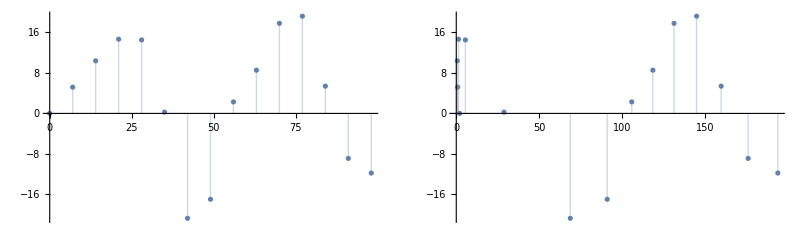

```mathematica
fitInfectedDynamic["ParameterTable"]
fitInfectedDynamic["RSquared"]
fitInfectedDynamic["AdjustedRSquared"]
fitInfectedDynamic["BestFitParameters"]
(*FitWithDataPlot[fitInfectedDynamic,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]*)
ResidualsPlot[fitInfectedDynamic]
```

## Modelo Final

```mathematica
finalFit = fitInfected2;
finalBeta = Values @@ finalFit["BestFitParameters"] *10
```

6.80064

```mathematica
modelSEIQRFinal = SetRateRules[modelSEIQR, <|NP[0] -> estimatedInitialSusceptiblePopulation,  β->finalBeta|>];
modelSEIQRFinal = SetInitialConditions[modelSEIQRFinal,
   <|SP[0] -> estimatedInitialSusceptiblePopulation -initialExposed- initialInfected-initialQuarantine,
    EP[0] -> initialExposed,
    IP[0] -> initialInfected,
    QP[0] -> initialQuarantine
    |>]; (* Subtrair do número da primeira semana epidemiológica*)
lsActualEquationsFinal = Join[modelSEIQRFinal["Equations"] //. KeyDrop[modelSEIQRFinal["RateRules"], {}], modelSEIQRFinal["InitialConditions"]];
ModelGridTableForm[modelSEIQRFinal]
ResourceFunction["GridTableForm"][List /@ lsActualEquationsFinal]
aSolFinal = NDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,0,60}]
```

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 235552.
2 | β | 6.80064
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==235540.
2 | EP[0]==2
3 | IP[0]==2
4 | QP[0]==8
5 | RP[0]==0|>

# | 1
1 | SP'[t]==0.2 QP[t]-0.0000288711 IP[t] SP[t]
2 | EP'[t]==-(2 EP[t])/13+0.0000288711 IP[t] SP[t]
3 | IP'[t]==EP[t]/13-(4 IP[t])/31
4 | QP'[t]==EP[t]/13-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | SP[0]==235540.
7 | EP[0]==2
8 | IP[0]==2
9 | QP[0]==8
10 | RP[0]==0

{{SP→InterpolatingFunction[…],EP→InterpolatingFunction[…],IP→InterpolatingFunction[…],QP→InterpolatingFunction[…],RP→InterpolatingFunction[…]}}

```mathematica
aSolForPeaks = Association@Flatten@ParametricNDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,0,60}, {β}] ;
allValues =Map[ParametricFunctionValues[#,<|β-> finalBeta|>, 60]&, aSolForPeaks]
peaks = Map[FindPeaks[Last/@#]&,allValues]
(*lsFinal = ParametricSolutionsPlots[modelSEIQRFinal["Stocks"],KeyTake[aSolFinal,GetPopulationSymbols[modelSEIQRFinal, __ ~~ "Population"]],{β},100,"Together"->True,optsFinal]*)
(*ListLinePlot[{allValues[[1]], peaks[[1]]}&,
Joined->{True, False},
PlotStyle->{Automatic, PointSize[.03]}]*)
```

<|SP→{{0,235540.},{1,235527.},{2,235508.},{3,235475.},{4,235417.},{5,235314.},{6,235128.},{7,234797.},{8,234206.},{9,233153.},{10,231287.},{11,228001.},{12,222289.},{13,212579.},{14,196694.},{15,172322.},{16,138596.},{17,98613.8},{18,60229.},{19,31669.8},{20,15413.5},{21,8131.2},{22,5366.42},{23,4342.92},{24,3883.78},{25,3597.63},{26,3372.75},{27,3179.28},{28,3008.47},{29,2856.63},{30,2721.34},{31,2600.55},{32,2492.5},{33,2395.61},{34,2308.51},{35,2230.01},{36,2159.06},{37,2094.78},{38,2036.38},{39,1983.19},{40,1934.64},{41,1890.21},{42,1849.48},{43,1812.05},{44,1777.6},{45,1745.83},{46,1716.48},{47,1689.34},{48,1664.2},{49,1640.88},{50,1619.23},{51,1599.11},{52,1580.39},{53,1562.96},{54,1546.72},{55,1531.59},{56,1517.47},{57,1504.29},{58,1492.},{59,1480.51},{60,1469.79}},EP→{{0,2.},{1,15.0505},{2,31.762},{3,58.866},{4,106.177},{5,190.296},{6,340.471},{7,608.646},{8,1086.99},{9,1938.14},{10,3445.94},{11,6095.92},{12,10688.5},{13,18453.7},{14,31034.2},{15,49989.},{16,75338.},{17,103422.},{18,126689.},{19,138290.},{20,137580.},{21,129229.},{22,118200.},{23,107218.},{24,97201.2},{25,88272.6},{26,80321.7},{27,73207.2},{28,66806.8},{29,61022.9},{30,55777.9},{31,51009.2},{32,46665.},{33,42702.},{34,39083.1},{35,35775.7},{36,32751.6},{37,29985.3},{38,27454.1},{39,25137.7},{40,23017.6},{41,21076.8},{42,19300.2},{43,17673.7},{44,16184.6},{45,14821.3},{46,13573.2},{47,12430.4},{48,11384.2},{49,10426.2},{50,9549.17},{51,8746.13},{52,8010.87},{53,7337.65},{54,6721.23},{55,6156.81},{56,5639.98},{57,5166.73},{58,4733.37},{59,4336.53},{60,3973.12}},IP→{{0,2.},{1,2.37958},{2,3.75304},{3,6.50294},{4,11.5462},{5,20.6201},{6,36.871},{7,65.9328},{8,117.852},{9,210.475},{10,375.307},{11,667.368},{12,1180.91},{13,2071.85},{14,3582.21},{15,6045.61},{16,9823.19},{17,15109.6},{18,21656.1},{19,28685.2},{20,35229.5},{21,40614.7},{22,44622.9},{23,47342.1},{24,48972.9},{25,49723.8},{26,49776.4},{27,49280.5},{28,48358.1},{29,47108.7},{30,45613.5},{31,43938.7},{32,42138.3},{33,40256.7},{34,38329.8},{35,36386.6},{36,34450.6},{37,32540.3},{38,30670.5},{39,28852.4},{40,27094.5},{41,25403.1},{42,23782.6},{43,22235.6},{44,20763.7},{45,19367.2},{46,18045.6},{47,16797.9},{48,15622.4},{49,14517.},{50,13479.3},{51,12506.7},{52,11596.4},{53,10745.5},{54,9951.23},{55,9210.54},{56,8520.56},{57,7878.44},{58,7281.38},{59,6726.69},{60,6211.77}},QP→{{0,8.},{1,6.33575},{2,6.08662},{3,7.31991},{4,10.6148},{5,17.2415},{6,29.5986},{7,52.0423},{8,92.379},{9,164.491},{10,292.87},{11,520.184},{12,919.163},{13,1608.99},{14,2771.24},{15,4646.31},{16,7467.19},{17,11286.},{18,15754.5},{19,20115.4},{20,23572.7},{21,25719.1},{22,26602.3},{23,26507.8},{24,25751.2},{25,24588.2},{26,23200.5},{27,21710.4},{28,20197.},{29,18710.2},{30,17280.2},{31,15924.1},{32,14650.5},{33,13462.7},{34,12360.2},{35,11340.5},{36,10399.9},{37,9533.85},{38,8737.53},{39,8006.1},{40,7334.78},{41,6719.01},{42,6154.42},{43,5636.94},{44,5162.75},{45,4728.32},{46,4330.37},{47,3965.87},{48,3632.05},{49,3326.34},{50,3046.39},{51,2790.03},{52,2555.29},{53,2340.35},{54,2143.53},{55,1963.31},{56,1798.3},{57,1647.2},{58,1508.84},{59,1382.15},{60,1266.14}},RP→{{0,0.},{1,1.18069},{2,2.35133},{3,3.84149},{4,6.10375},{5,9.87362},{6,16.4235},{7,28.001},{8,48.6023},{9,85.338},{10,150.836},{11,267.401},{12,474.056},{13,837.879},{14,1470.67},{15,2549.06},{16,4327.54},{17,7120.18},{18,11223.},{19,16791.},{20,23755.8},{21,31858.2},{22,40759.9},{23,50141.2},{24,59742.7},{25,69369.7},{26,78880.5},{27,88174.5},{28,97181.4},{29,105853.},{30,114159.},{31,122079.},{32,129605.},{33,136735.},{34,143470.},{35,149819.},{36,155791.},{37,161398.},{38,166653.},{39,171572.},{40,176170.},{41,180463.},{42,184465.},{43,188194.},{44,191663.},{45,194889.},{46,197886.},{47,200668.},{48,203249.},{49,205641.},{50,207858.},{51,209910.},{52,211809.},{53,213565.},{54,215189.},{55,216690.},{56,218076.},{57,219355.},{58,220536.},{59,221626.},{60,222631.}}|>

<|SP→{{1,235540.}},EP→{{20,138290.}},IP→{{27,49776.4}},QP→{{1,8.},{23,26602.3}},RP→{{61,222631.}}|>

```mathematica
Clear[PadRealData];
PadRealData[aData:Association[(_String->_?VectorQ)..],incubationPeriod_?IntegerQ,infectiousPeriod_?IntegerQ]:=Block[{},Join[ConstantArray[0,incubationPeriod+infectiousPeriod],#]&/@aData];
```

```mathematica
(*Map[ParametricSolutionsPlots[#,<|β-> finalBeta|>, 100]&, aSolFinal]*)
(*PadRealData[peaks,13,7.75]*)
(*Show[lsFinal, peaks,PlotStyle->{Blue,Black,Red}]*)
(*Show[Plot[allValues,Joined->False,PlotRange->All]]*)
optsFinal={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
DynamicModule[{incubationPeriod=13,infectionPeriod=8,nWeeks=60,padOffset=-8},
DynamicModule[{modelSEIQR=modelSEIQRFinal,lsFinal},
lsFinal = ParametricSolutionsPlots[modelSEIQR["Stocks"],#,None,nWeeks,"Together"->True,optsFinal]&/@GroupBy[Normal@aSolFinal,#[[1,1]]&,Association];
(*Show[List@Plot[Map[Identity[#]&,Values[aSolFinal]],{t,0,100}, PlotRange->All,PlotLegends->None,PlotTheme->"Detailed"], ListPlot[peaks,PlotStyle-> {Red,Black,Blue}]]]]*)
Show[lsFinal[[1,1]], ListPlot[Labeled[#,#]&/@peaks, PlotLabels->Above,PlotLegends->None]]
]
]
```